```mathematica
clear[Subscript[G, 1],Subscript[G, 2],Subscript[η, 1],Subscript[η, 2],Subscript[η, 3],Subscript[η, 4]]
```

clear[4,6,0.9,η_2,0.6,0.9]

```mathematica
ClearAll["Global`*"]
```

```mathematica
rns2ni2 = ((-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2 (1+α^2)+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+(1+2 α^2) Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]+(-1+Subscript[G, 2] (1+(-1+Subscript[G, 1]) Subscript[η, 1])) (-1+Subscript[G, 2] (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]^2+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))-2 ((√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])) (√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) (√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))))/(-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))
```

((-1+G_2)^2 (1+η_1 (-2 (1+α^2)+(1+2 α^2) G_1+η_1+(-1+G_1) (-2 α^2+(1+2 α^2) G_1) η_1)) η_3^2+(-1+G_2 (1+(1+α^2) (-1+G_1) η_1)) η_4+(-1+G_2 (1+(-1+G_1) η_1)) (-1+G_2 (1+(1+2 α^2) (-1+G_1) η_1)) η_4^2+(-1+G_2) η_3 (1+(-1+G_1) η_1 (1+α^2-2 α^2 (-1+G_1) G_2 η_1 η_4))-2 ((√(G_2 η_3) √((-1+G_2) η_4)+√((-1+G_1) (-1+G_2) η_1 η_3) √((-1+G_1) G_2 η_1 η_4)) (√(-((-1+G_2) (-1+η_1) η_3)) √(-G_2 (-1+η_1) η_4)+√(G_1 (-1+G_2) η_1 η_3) √(G_1 G_2 η_1 η_4))+α^2 √((-1+G_1) (-1+G_2) η_1 η_3) √((-1+G_1) G_2 η_1 η_4) (√(G_2 η_3) √((-1+G_2) η_4)+√(-((-1+G_2) (-1+η_1) η_3)) √(-G_2 (-1+η_1) η_4)+√(G_1 (-1+G_2) η_1 η_3) √(G_1 G_2 η_1 η_4))))/(-η_4+(1+(1+α^2) (-1+G_1) η_1) ((-1+G_2) η_3+G_2 η_4))

```mathematica
Quit
```

```mathematica
(*For Subscript[G, 1] = 2 & Subscript[η, 1] = Subscript[η, 2] = Subscript[η, 3] = 1, i.e. no loss *)
Subscript[η, 1] = 1;
Subscript[η, 3] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 2;
α = 5;
ra1 = NumberForm[Simplify[((-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2 (1+α^2)+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+(1+2 α^2) Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]+(-1+Subscript[G, 2] (1+(-1+Subscript[G, 1]) Subscript[η, 1])) (-1+Subscript[G, 2] (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]^2+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))-2 ((√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])) (√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) (√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))))/(-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

77/(-28+54 G_2)

```mathematica
Quit
```

```mathematica
(*For Subscript[G, 1] = 2 & Subscript[η, 1] = Subscript[η, 2] = Subscript[η, 3] = 1, i.e. no loss *)
Subscript[η, 1] = 0.9;
Subscript[η, 3] = 0.9;
Subscript[η, 4] = 0.9;
Subscript[G, 1] = 2;
α = 5;
ra2 = NumberForm[Simplify[((-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2 (1+α^2)+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+(1+2 α^2) Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]+(-1+Subscript[G, 2] (1+(-1+Subscript[G, 1]) Subscript[η, 1])) (-1+Subscript[G, 2] (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]^2+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))-2 ((√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])) (√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) (√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))))/(-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.138+0.107 G_2-0.003 G_2^2)/(-0.520+1.000 G_2)

```mathematica
Quit
```

```mathematica
(*For Subscript[G, 1] = 2 & Subscript[η, 1] = Subscript[η, 2] = Subscript[η, 3] = 1, i.e. no loss *)
Subscript[η, 1] = 0.8;
Subscript[η, 3] = 0.85;
Subscript[η, 4] = 0.7;
Subscript[G, 1] = 2;
α = 5;
ra3 = NumberForm[Simplify[((-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2 (1+α^2)+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+(1+2 α^2) Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]+(-1+Subscript[G, 2] (1+(-1+Subscript[G, 1]) Subscript[η, 1])) (-1+Subscript[G, 2] (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]^2+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))-2 ((√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])) (√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) (√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))))/(-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.047-0.186 G_2+0.043 G_2^2)/(-0.569+1.000 G_2)

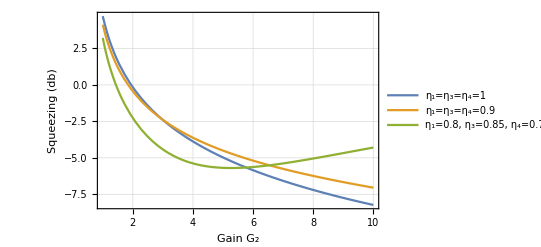

```mathematica
Plot[{10Log10[("77")/("-28"+"54" Subscript[G, "2"])](*1, 1, 1*),10Log10[("1.138"+"0.107" Subscript[G, "2"]-"0.003" Subscript[G, "2"]^("2"))/("-0.520"+"1.000" Subscript[G, "2"])](*0.9, 0.9, 0.9*),10Log10[("1.047"-"0.186" Subscript[G, "2"]+"0.043" Subscript[G, "2"]^("2"))/("-0.569"+"1.000" Subscript[G, "2"])](*0.8, 0.85, 0.7*)},{Subscript[G, 2],1,10},PlotStyle->ScientificForm(*PlotRange->{{1,10},{-18,12}}*) (*Y-axis between 0 and 1*),PlotLegends->{"η_1=η_3=η_4=1","η_1=η_3=η_4=0.9","η_1=0.8, η_3=0.85, η_4=0.7"},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["Gain G_2"],HoldForm["R_ns2ni2 vs G_2 for G_1 = 2, α = 5"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
Quit
```

```mathematica
(*For Subscript[G, 1] = 2 & Subscript[η, 1] = Subscript[η, 2] = Subscript[η, 3] = 1, i.e. no loss *)
Subscript[η, 1] = 0.9;
Subscript[η, 3] = 0.9;
Subscript[G, 1] = 2.6;
Subscript[G, 2] = 6.5;
α = 5;
rb1 = NumberForm[Simplify[((-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2 (1+α^2)+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+(1+2 α^2) Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]+(-1+Subscript[G, 2] (1+(-1+Subscript[G, 1]) Subscript[η, 1])) (-1+Subscript[G, 2] (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]^2+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))-2 ((√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])) (√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) (√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))))/(-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(18.625-45.967 η_4+28.833 η_4^2)/(0.765+1.000 η_4)

```mathematica
(*For Subscript[G, 1] = 2 & Subscript[η, 1] = Subscript[η, 2] = Subscript[η, 3] = 1, i.e. no loss *)
Subscript[η, 1] = 0.8;
Subscript[η, 3] = 0.7;
Subscript[G, 1] = 2.6;
Subscript[G, 2] = 6.5;
α = 5;
rb2 = NumberForm[Simplify[((-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2 (1+α^2)+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+(1+2 α^2) Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]+(-1+Subscript[G, 2] (1+(-1+Subscript[G, 1]) Subscript[η, 1])) (-1+Subscript[G, 2] (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]^2+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))-2 ((√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])) (√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) (√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))))/(-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity, 3}]
```

(10.665-33.097 η_4+26.779 η_4^2)/(0.595+1.000 η_4)

```mathematica
(*For Subscript[G, 1] = 2 & Subscript[η, 1] = Subscript[η, 2] = Subscript[η, 3] = 1, i.e. no loss *)
Subscript[η, 1] = 0.8;
Subscript[η, 3] = 0.6;
Subscript[G, 1] = 2.6;
Subscript[G, 2] = 6.5;
α = 5;
rb3 = NumberForm[Simplify[((-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2 (1+α^2)+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+(1+2 α^2) Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]+(-1+Subscript[G, 2] (1+(-1+Subscript[G, 1]) Subscript[η, 1])) (-1+Subscript[G, 2] (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]^2+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))-2 ((√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])) (√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) (√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))))/(-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(7.909-28.226 η_4+26.779 η_4^2)/(0.510+1.000 η_4)

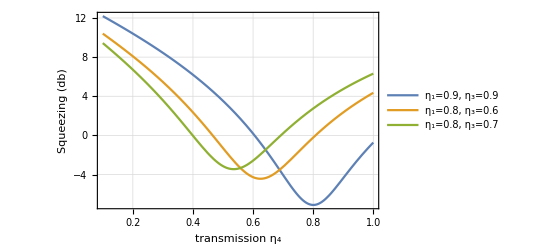

```mathematica
Plot[{10Log10[("18.625"-"45.967" Subscript[η, "4"]+"28.833" Subscript[η, "4"]^("2"))/("0.765"+"1.000" Subscript[η, "4"])](*0.9, 0.9*),10Log10[("10.665"-"33.097" Subscript[η, "4"]+"26.779" Subscript[η, "4"]^("2"))/("0.595"+"1.000" Subscript[η, "4"])](*0.8, 0.7*),10Log10[("7.909"-"28.226" Subscript[η, "4"]+"26.779" Subscript[η, "4"]^("2"))/("0.510"+"1.000" Subscript[η, "4"])](*0.8, 0.6*)},{Subscript[η, 4],0.1,1},PlotLegends->{"η_1=0.9, η_3=0.9","η_1=0.8, η_3=0.6","η_1=0.8, η_3=0.7"},PlotStyle->Automatic(*PlotRange->{{1,10},{-18,12}}*) (*Y-axis between 0 and 1*),Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_4"],HoldForm["R_ns2ni2 vs η_4 for G_1= 2.6, G_2= 6.5"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
Quit
```

```mathematica
Subscript[η, 1] = 0.9;
Subscript[η, 4] = 0.9;
Subscript[G, 1] = 4;
Subscript[G, 2] = 6;
α = 5;
rc1 = NumberForm[Simplify[((-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2 (1+α^2)+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+(1+2 α^2) Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]+(-1+Subscript[G, 2] (1+(-1+Subscript[G, 1]) Subscript[η, 1])) (-1+Subscript[G, 2] (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]^2+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))-2 ((√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])) (√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) (√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))))/(-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(41.171-76.843 η_3+36.013 η_3^2)/(1.077+1.000 η_3)

```mathematica
Subscript[η, 1] = 0.8;
Subscript[η, 4] = 0.8;
Subscript[G, 1] = 4;
Subscript[G, 2] = 6;
α = 5;
rc2 = NumberForm[Simplify[((-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2 (1+α^2)+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+(1+2 α^2) Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]+(-1+Subscript[G, 2] (1+(-1+Subscript[G, 1]) Subscript[η, 1])) (-1+Subscript[G, 2] (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]^2+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))-2 ((√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])) (√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) (√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))))/(-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(29.918-62.530 η_3+33.038 η_3^2)/(0.957+1.000 η_3)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 4] = 0.75;
Subscript[G, 1] = 4;
Subscript[G, 2] = 6;
α = 5;
rc3 = NumberForm[Simplify[((-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2 (1+α^2)+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+(1+2 α^2) Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]+(-1+Subscript[G, 2] (1+(-1+Subscript[G, 1]) Subscript[η, 1])) (-1+Subscript[G, 2] (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]^2+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))-2 ((√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])) (√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) (√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))))/(-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(23.959-53.244 η_3+30.060 η_3^2)/(0.897+1.000 η_3)

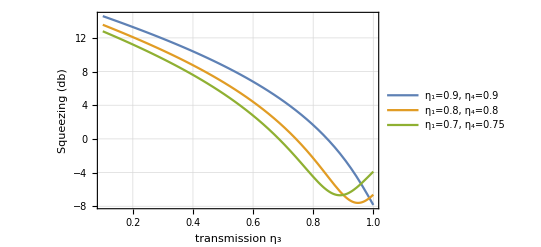

```mathematica
Plot[{10Log10[("41.171"-"76.843" Subscript[η, "3"]+"36.013" Subscript[η, "3"]^("2"))/("1.077"+"1.000" Subscript[η, "3"])],10Log10[("29.918"-"62.530" Subscript[η, "3"]+"33.038" Subscript[η, "3"]^("2"))/("0.957"+"1.000" Subscript[η, "3"])],10Log10[("23.959"-"53.244" Subscript[η, "3"]+"30.060" Subscript[η, "3"]^("2"))/("0.897"+"1.000" Subscript[η, "3"])]},{Subscript[η, 3],0.1,1},PlotStyle->Automatic(*PlotRange->{{1,10},{-18,12}}*) (*Y-axis between 0 and 1*),PlotLegends->{"η_1=0.9, η_4=0.9","η_1=0.8, η_4=0.8","η_1=0.7, η_4=0.75"},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_3"],HoldForm["R_ns2ni2 vs η_3 for G_1=4, G_2=6"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
Quit
```

```mathematica
Subscript[η, 3] = 0.9;
Subscript[η, 4] = 0.9;
Subscript[G, 1] = 4;
Subscript[G, 2] = 6;
α = 5;
rd1 = NumberForm[Simplify[((-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2 (1+α^2)+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+(1+2 α^2) Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]+(-1+Subscript[G, 2] (1+(-1+Subscript[G, 1]) Subscript[η, 1])) (-1+Subscript[G, 2] (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]^2+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))-2 ((√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])) (√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) (√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))))/(-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.001+0.077 η_1+0.586 η_1^2)/(0.012+1.000 η_1)

```mathematica
Subscript[η, 3] = 0.7;
Subscript[η, 4] = 0.75;
Subscript[G, 1] = 4;
Subscript[G, 2] = 6;
α = 5;
rd2 = NumberForm[Simplify[((-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2 (1+α^2)+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+(1+2 α^2) Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]+(-1+Subscript[G, 2] (1+(-1+Subscript[G, 1]) Subscript[η, 1])) (-1+Subscript[G, 2] (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]^2+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))-2 ((√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])) (√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) (√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))))/(-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.003+0.328 η_1+0.814 η_1^2)/(0.012+1.000 η_1)

```mathematica
Subscript[η, 3] = 0.8;
Subscript[η, 4] = 0.75;
Subscript[G, 1] = 4;
Subscript[G, 2] = 6;
α = 5;
rd3 = NumberForm[Simplify[((-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2 (1+α^2)+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+(1+2 α^2) Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]+(-1+Subscript[G, 2] (1+(-1+Subscript[G, 1]) Subscript[η, 1])) (-1+Subscript[G, 2] (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]^2+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))-2 ((√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])) (√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) (√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))))/(-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.003+0.168 η_1+0.270 η_1^2)/(0.012+1.000 η_1)

```mathematica
Subscript[η, 3] = 0.7;
Subscript[η, 4] = 0.85;
Subscript[G, 1] = 4;
Subscript[G, 2] = 6;
α = 5;
rd4 = NumberForm[Simplify[((-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2 (1+α^2)+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+(1+2 α^2) Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]+(-1+Subscript[G, 2] (1+(-1+Subscript[G, 1]) Subscript[η, 1])) (-1+Subscript[G, 2] (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]^2+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))-2 ((√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])) (√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) (√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))))/(-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.004+0.514 η_1+1.825 η_1^2)/(0.012+1.000 η_1)

```mathematica
Subscript[η, 3] = 0.7;
Subscript[η, 4] = 0.9;
Subscript[G, 1] = 4;
Subscript[G, 2] = 6;
α = 5;
rd5 = NumberForm[Simplify[((-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2 (1+α^2)+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+(1+2 α^2) Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]+(-1+Subscript[G, 2] (1+(-1+Subscript[G, 1]) Subscript[η, 1])) (-1+Subscript[G, 2] (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 4]^2+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))-2 ((√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])) (√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) (√(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4])+√(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))))/(-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.004+0.649 η_1+2.457 η_1^2)/(0.012+1.000 η_1)

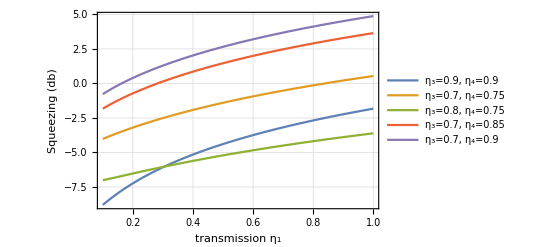

```mathematica
Plot[{10Log10[("0.001"+"0.077" Subscript[η, "1"]+"0.586" Subscript[η, "1"]^("2"))/("0.012"+"1.000" Subscript[η, "1"])],10Log10[("0.003"+"0.328" Subscript[η, "1"]+"0.814" Subscript[η, "1"]^("2"))/("0.012"+"1.000" Subscript[η, "1"])],10Log10[("0.003"+"0.168" Subscript[η, "1"]+"0.270" Subscript[η, "1"]^("2"))/("0.012"+"1.000" Subscript[η, "1"])],10Log10[("0.004"+"0.514" Subscript[η, "1"]+"1.825" Subscript[η, "1"]^("2"))/("0.012"+"1.000" Subscript[η, "1"])],10Log10[("0.004"+"0.649" Subscript[η, "1"]+"2.457" Subscript[η, "1"]^("2"))/("0.012"+"1.000" Subscript[η, "1"])]},{Subscript[η, 1],0.1,1},PlotStyle->Automatic(*PlotRange->{{1,10},{-18,12}}*) (*Y-axis between 0 and 1*),PlotLegends->{"η_3=0.9, η_4=0.9","η_3=0.7, η_4=0.75","η_3=0.8, η_4=0.75","η_3=0.7, η_4=0.85","η_3=0.7, η_4=0.9"},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_1"],HoldForm["R_ns2ni2 vs η_1 for G_1=4, G_2=6"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```